```mathematica
LagrangePolynomial[x0_,f0_] :=
Module[{xi=x0,fi=f0,n,m,polynomial},
n=Length[xi];
m=Length[fi];
If[n≠  m,Print["List of points and functions values are not of same size"];
Return[];];
For[i=1,i≤ n,i++,
L[i,x_]= (Product[( x-xi[[j]])/(xi[[i]]-xi[[j]]),{j,1,i-1}])*
(Product[(x-xi[[j]])/(xi[[i]]-xi[[j]]),{j,i+1,n}]);];
polynomial[x_]=Sum[L[k,x]*fi[[k]],{k,1,n}];
Return[polynomial[x]];]


nodes={0,1,3};
values={1,3,55};
lagrangePolynomial[x_]=LagrangePolynomial[nodes,values]
```

1/3 (1-x) (3-x)+3/2 (3-x) x+55/6 (-1+x) x

```mathematica
Expand[%]
```

1-6 x+8 x^2

```mathematica
nodes={0,1,3};
values={1,3};
lagrangePolynomial[x_]=LagrangePolynomial[nodes,values]
```

List of points and functions values are not of same size

```mathematica
nodes={1,3,5,7,9};
values={N[Log[1]],N[Log[3]],N[Log[5]],N[Log[7]],N[Log[9]]};
lagrangePolynomial[x_]=LagrangePolynomial[nodes,values]
```

0.+0.0114439 (5-x) (7-x) (9-x) (-1+x)+0.0251475 (7-x) (9-x) (-3+x) (-1+x)+0.0202699 (9-x) (-5+x) (-3+x) (-1+x)+0.00572194 (-7+x) (-5+x) (-3+x) (-1+x)

```mathematica
Simplify[%]
```

-0.987583+1.18991 x-0.223608 x^2+0.0221231 x^3-0.000844369 x^4

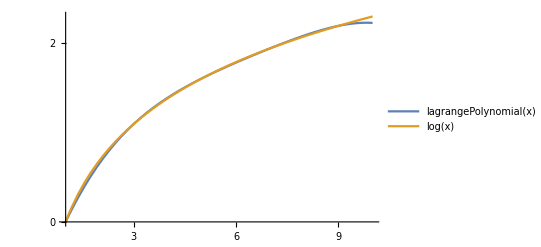

```mathematica
Plot[{lagrangePolynomial[x],Log[x]},{x,1,10},
Ticks-> {Range[0,10]},PlotLegends-> "Expressions"]
```

```mathematica
nodes={-1,0,1,2};
values={};
lagrangePolynomial[x_]=LagrangePolynomial[nodes,values]
```

List of points and functions values are not of same size

```mathematica
nodes={-1,0,1,2};
values={5,1,1,11};
lagrangePolynomial[x_]=LagrangePolynomial[nodes,values]
```

-5/6 (1-x) (2-x) x+1/2 (1-x) (2-x) (1+x)+1/2 (2-x) x (1+x)+11/6 (-1+x) x (1+x)

```mathematica
Simplify[%]
```

1-3 x+2 x^2+x^3

```mathematica
lagrangePolynomial[1.5]
```

4.375